```mathematica
P[q_,R_,NN_]:=NIntegrate[Exp[-(q*R)^2*Sqrt[(n-m)^2]/(2NN)],{n,0,NN},{m,0,NN}]/NN^2
```

```mathematica
Integrate[(N-n)*n,{n,0,N}]/N^2
```

N/6

```mathematica
Integrate[Exp[-(q*R)^2*Sqrt[(n-m)^2]/(2NN)*(1-Sqrt[(n-m)^2]/(NN))],{n,0,NN},{m,0,NN},Assumptions->NN>0]/NN^2
```

(ⅇ^(-1/8 q^2 R^2) √(2 π) Erfi[(q R)/(2 √2)])/(q R)

```mathematica
Pring[q_,R_]:=(ⅇ^(-1/8 q^2 R^2) √(2 π) Erfi[(q R)/(2 √2)])/(q R)
```

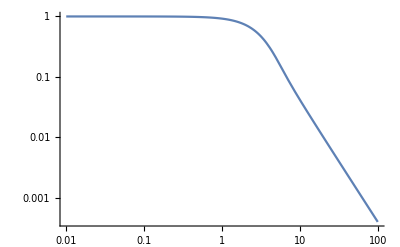

```mathematica
LogLogPlot[Pring[q,1],{q,0.01,100}]
```

```mathematica
Debye[q_,R_]:=2*((Exp[-(q*R)^2/2]-1+(q*R)^2/2)/((q*R)^2/2)^2)
```

```mathematica
LogLogPlot[{P[q,1,10],Debye[q,1]},{q,0.1,10}]
```

$Aborted

```mathematica
fqr[q_,R_,mu_,Wi_,psi_]:=mu+Pi^4/180*(Cos[psi]*Wi*mu)^2*(1+mu-(mu/2)^2-2*mu^3+mu^4)
```

```mathematica
fqr[q,R,mu,Wi,psi]
```

mu+1/180 mu^2 (1+mu-mu^2/4-2 mu^3+mu^4) π^4 Wi^2 Cos[psi]^2

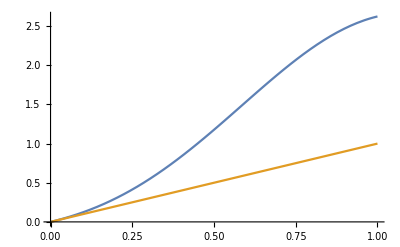

```mathematica
Plot[{fqr[1,3,mu,2,0*Pi/2],fqr[1,3,mu,2,Pi/2]},{mu,0,1}]
```

```mathematica
CForm[fqr[q,R,mu,Wi,psi]]
```

mu + (Power(mu,2)*(1 + mu - Power(mu,2)/4. - 2*Power(mu,3) + Power(mu,4))*Power(Pi,4)*Power(Wi,2)*
      Power(Cos(psi),2))/180.

```mathematica
Prouse[q_,R_,Wi_,psi_,NN_]:=NIntegrate[Exp[-(q*R)^2/2*fqr[q,R,Sqrt[(n-m)^2]/(NN),Wi,psi]],{n,0,NN},{m,0,NN}]/NN^2
```

```mathematica
LogLogPlot[{Prouse[q,1,2,0,10],Prouse[q,1,2,Pi/2,10]},{q,0.1,40}]
```

$Aborted

```mathematica
Integrate[Exp[-(q*R)^2/2*fqr[q,R,Sqrt[(n-m)^2]/(NN),Wi,psi]],{n,0,NN},{m,0,NN},Assumptions->NN>0]/NN^2
```

Integrate[ⅇ^(-1/2 q^2 R^2 (Abs[m-n]/NN+((m-n)^2 π^4 Wi^2 (4 (m-n)^4-(m-n)^2 NN^2+4 NN^4+4 NN^3 Abs[m-n]-8 NN Abs[m-n]^3) Cos[psi]^2)/(720 NN^6))),{n,0,NN},{m,0,NN},Assumptions→NN>0]/NN^2

```mathematica
Gerade[x_,x1_,y1_,x2_,y2_]:=(y2-y1)/(x2-x1)*(x-x1)+y1
```

```mathematica
Gerade[x,0,0,nu,b*nu]
```

b x

```mathematica
Collect[Gerade[x,nu,b*nu,1-nu,b*nu+c*(1-2*nu)],{x,nu}]
```

(b-c) nu+c x

```mathematica
Collect[Gerade[x,1-nu,c*(1-2*nu)+b*nu,1,c*(1-2*nu)+2*b*nu],{x,nu}]
```

-b+c+(2 b-2 c) nu+b x

```mathematica
qrnm[x_,b_,c_,nu_]:=Piecewise[{{b*x,x<=nu},{c-2 c nu+b (-1+2 nu+x),x>=1-nu}},b nu+c (-nu+x)]*Sqrt[b/(c+2 b nu-2 c nu)]
```

```mathematica
qrnmring[x_,b_,c_,nu_]:=qrnm[x,b,c,nu]*(qrnm[1,b,c,nu]-qrnm[x,b,c,nu])
```

```mathematica
FullSimplify[qrnmring[1/2,b,c,nu],nu<1/2&&nu>0]
```

1/4 b (c+2 b nu-2 c nu)

```mathematica
D[b*x*(b-b*x),x]
```

-b^2 x+b (b-b x)

```mathematica
Limit[%,x->0]
```

1/4 b (c+2 b nu-2 c nu)

```mathematica
FullSimplify[D[qrnmring[x,b,c,nu],x],Assumptions->nu>0&&nu≤1/2&&x<=nu&&x≤1]
```

b^2-(2 b^3 x)/(c+2 b nu-2 c nu)

```mathematica
FullSimplify[D[qrnm[x,b,c,nu],x],Assumptions->nu>0&&nu≤1/2&&x>nu&&x<1-nu]
```

c √(b/(c+2 b nu-2 c nu))

```mathematica
Limit[%,x->0]
```

b^2

```mathematica
Solve[x*(x0-x)==ym,x]
```

{{x→1/2 (x0-√(x0^2-4 ym))},{x→1/2 (x0+√(x0^2-4 ym))}}

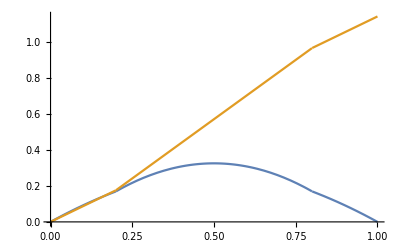

```mathematica
Plot[{qrnmring[x,1,1.5,0.2],qrnm[x,1,1.5,0.2]},{x,0,1}]
```